# Report Project 1

Course code: IX1500
Date: 2018-09-13

Josef Federspiel, joseffe@kth.se
Linus Bein Fahlander, linusfa@kth.se

## Code Section

#### Generating deck and sorted hands with value as sort key

```mathematica
ClearAll["`*"]
orderQ[card1_,card2_]:=card1⟦1⟧<card2⟦1⟧;
valueSort[hand_]:=Sort[hand,orderQ];
```

```mathematica
deck1=Join[Table[h[i],{i,9,14}],Table[d[i],{i,9,14}],Table[c[i],{i,9,14}],Table[s[i],{i,9,14}]];
deck2=Flatten[Join[Table[h[i],{i,9,14}],Table[d[i],{i,9,14}],Table[c[i],{i,9,14}],Table[s[i],{i,9,14}]]];
deckF=Flatten[Join[deck1, deck2]];
```

```mathematica
handsF = valueSort/@Subsets[deckF,{5}];
```

#### Declaring matching functions for each type of hand

```mathematica
pair[h_] := MatchQ[h, {___, x_, x_, ___}];
twoPair[h_]:= MatchQ[h, {___, x_, x_, ___, y_, y_, ___}];
three[h_]:=MatchQ[h, {___, x_,x_, x_, ___}];
four[h_]:=MatchQ[h, {___, x_, x_, x_, x_, ___}];
full[h_]:=MatchQ[h, {x_,x_,y_,y_,y_} /; x≠y] || MatchQ[h, {x_,x_,x_,y_,y_} /; x≠y];
straight[h_]:=MatchQ[h-h⟦1⟧, {0,1,2,3,4}];
flush[h_]:=MatchQ[h, {x_,x_,x_,x_,x_}];
five[h_] := flush[h];
straightflush[h_]:=(straight[First /@ h]) && (flush[Head /@ h]);
```

#### Declaring global counters and ranked comparison function

```mathematica
SF=FLUSH=STRAIGHT=FULLHOUSE=FIVE=FOUR=THREE=
TWOPAIR=PAIR=NONE = 0;
testResults = {};
getResult[h_]:= If[straightflush[h],SF++,If[flush[Head /@ h],FLUSH++,If[five[First/@h], FIVE++,If[straight[First /@ h],STRAIGHT++,If[full[First /@ h],FULLHOUSE++,If[four[First /@ h],FOUR++,If[three[First /@ h], THREE++,
If[twoPair[First /@ h], TWOPAIR++,
If[pair[First /@ h], PAIR++, NONE++]]]]]]]]];
```

#### Running each hand through comparison function and display results

```mathematica
SF=FLUSH=STRAIGHT=FULLHOUSE=FIVE=FOUR=THREE=
TWOPAIR=PAIR=NONE= 0;
testResults = {};
i = 1;
For[i,i<=Length[handsF],i++,getResult[handsF[[i]]]];

StringForm["Straight Flush:``\nFlush:``\nStraight:``\nFull House:``",SF,FLUSH,STRAIGHT,FULLHOUSE]
StringForm["Five:``\nFour:``\nThree:``\nTwo Pair:``\nPair:``",FIVE,FOUR,THREE,TWOPAIR, PAIR]
StringForm["None:``\nTotal:``",NONE,Length[handsF]]
```

Straight Flush:256
Flush:2912
Straight:65280
Full House:47040

Five:336
Four:16800
Three:215040
Two Pair:375840
Pair:858240

None:130560
Total:1712304

## A) Odds and discussion

### Summery

#### Task

Assume that you play a variant of a poker game with five cards that is using a subset of two ordinary deck of cards. The subset considered is cards valued 9,10,J,Q,K,A from the two decks, in total 48 cards.

Calculate the exact probability of the following hands using the  census method.

one pair

two pairs

three of a kind

four of a kind

five of a kind

full hand

straight

flush

straight flush

nothing

If a given hand contains different valued hands only one (the highest rank) is considered.

Example :

h={♣10,♡10,♢K,♢K,♠K}

⇒onepairQ(h)=false,twopairsQ(h)=false,threeofakindQ(h)=false,fullhandQ(h)=true

Notice that the different sets of hands are supposed to be pairwise disjoint, e.g. {three of a kind}∩{full house}=∅. Check all different possibilities. This is an easy way of discover programming errors.

Compare and discuss the probabilities of the above variant poker game to the probabilities for a normal poker game with a standard 52 card deck.

#### Results

n_Total represents  the total amount of hands possible with the deck.
The chance of drawing a specific hand can be described as a quotient of the amount of possible hands containing the specifed cards divided  by the total amount of possible hands.

```mathematica
Subscript[n, Total]=Binomial[48, 5]=1712304
```

Straight Flush:

Odds_StraightFlush=n_StraightFlush/n_Total≈0.015%

Flush:

Odds_Flush=n_Flush/n_Total≈0.17%

Straight:

Odds_Straight=n_Straight/n_Total≈3.81%

Full House:

Odds_FullHouse=n_FullHouse/n_Total≈2.71%

Five of a Kind:

Odds_FiveKind=n_FiveKind/n_Total≈0.0196%

Four of a Kind:

Odds_FourKind=n_FourKind/n_Total≈0.981%

Three of a Kind:

Odds_ThreeKind=n_ThreeKind/n_Total≈12.6%

Two Pair:

Odds_TwoPair=n_TwoPair/n_Total≈21.9%

Pair:

Odds_Pair=n_Pair/n_Total≈50.1%

High Card:

Odds_HighCard=n_HighCard/n_Total≈7.62%

### Strategy

Our strategy for approaching the problem was to first generating all possible hands and saving them in a list. Then we constructed functions for matching a hand to one of the hand types described in the task. After that a comparison function was written that in order of value the hand was tested against the matching functions, where the first match would increase an associated counter and the comparison would end. This way we avoided hands returning positive answers on several matching functions and the value of the counters represented the exact amount of hands of the given type. We did this to circumvent having to iterate through the list of hands more than once.

### Discussion

The probabilities of the given deck make it very likely to draw a hand which contains a pair or above. For example the probability of a hand containing a pair is roughly 50% with our deck when with a normal deck the probability is about 42% . Both scenarios are quiet close to one another, its when we start looking towards the less common hands we see a large difference in probability.
The odds of drawing a hand containing a two pair with our deck is approximately 21.9% and with a normal deck of cards the odds of drawing the same hand is 4.7% . With our deck the average value of a hand is much higher when compared to the average hand drawn from a normal deck.

### Code Section

#### Straight Flush :

```mathematica
oddsSF=SF/Length[handsF];
StringForm["Odds: ``%",NumberForm[N[oddsSF]100, 3]]
```

Odds: 0.015%

#### Flush :

```mathematica
oddsFlush=FLUSH/Length[handsF];
StringForm["Odds: ``%",NumberForm[N[oddsFlush]100, 3]]
```

Odds: 0.17%

#### Straight :

```mathematica
oddsStraight=STRAIGHT/Length[handsF];
StringForm["Odds: ``%",NumberForm[N[oddsStraight]100, 3]]
```

Odds: 3.81%

#### Full House :

```mathematica
oddsFH=FULLHOUSE/Length[handsF];
StringForm["Odds: ``%",NumberForm[N[oddsFH]100, 3]]
```

Odds: 2.75%

#### Five of a Kind :

```mathematica
oddsFive=FIVE/Length[handsF];
StringForm["Odds: ``%",NumberForm[N[oddsFive]100, 3]]
```

Odds: 0.0196%

#### Four of a Kind :

```mathematica
oddsFour=FOUR/Length[handsF];
StringForm["Odds: ``%",NumberForm[N[oddsFour]100, 3]]
```

Odds: 0.981%

#### Three of a Kind :

```mathematica
oddsThree=THREE/Length[handsF];
StringForm["Odds: ``%",NumberForm[N[oddsThree]100, 3]]
```

Odds: 12.6%

#### Two Pair :

```mathematica
oddsTwoP=TWOPAIR/Length[handsF];
StringForm["Odds: ``%",NumberForm[N[oddsTwoP]100, 3]]
```

Odds: 21.9%

#### Pair :

```mathematica
oddsPair=PAIR/Length[handsF];
StringForm["Odds: ``%",NumberForm[N[oddsPair]100, 3]]
```

Odds: 50.1%

#### High Card :

```mathematica
oddsNone=NONE/Length[handsF];
StringForm["Odds: ``%",NumberForm[N[oddsNone]100, 3]]
```

Odds: 7.62%

## B) Combinatorial Calculus

### Task

Consider the following  combinatorial calculus of the probability of getting four of a kind. In this case we are dealing with sampling without replacement and without regard to order. First choose one of six possibilities {9,…,A} to be the kind value x, then we choose four out of the eight x and finally we add a last card from the remaining 40. The multiplication principle gives the result.

```mathematica
Subscript[n, value]=Binomial[6, 1],Subscript[n, 4cards]=Binomial[8, 4], Subscript[n, last]=Binomial[40, 1]
```

```mathematica
Subscript[n, 4]=Subscript[n, value] Subscript[n, 4cards] Subscript[n, last]=Binomial[6, 1] Binomial[8, 4]Binomial[40, 1]
```

```mathematica
∴Subscript[P, 4]=Subscript[n, 4]/Subscript[n, tot]=(Binomial[6, 1] Binomial[8, 4]Binomial[40, 1])/Binomial[48, 5]=35/3243≈0.0107925
```

Now , verify this probability by your census in part a)
Add combinatorial calculus for flush, straight, full house and 3 of a kind to your report. Also verify these calculations by your census.

### Results

#### Total:

n_Total=Binomial[48, 5]=1712304

#### Straight Flush:

To find the amount of hands containing a straight flush we select the first number from a possible combination of 16 cards , 9s and 10s. For the 2nd slot we can choose one out of 2 cards since the suit of the card needs to match the card in the first position and the value of the card has to be the value of the first card plus one. The same is true for the remaining cards in the hand. 
The multiplication principle then gives us:

n_StraightFlush=Binomial[16, 1] Binomial[2, 1]^4=256
odds_StraightFlush=n_StraightFlush/n_Total≈0.00015=0.015%

#### Flush:

To calculate the amount of hands containing a flush we must choose 5 cards from the 12 cards in that a suit. Since there are four different suits we multiply the amount of possible hands by four. Then we need to subtract the hands containing a straight flush since that hand is considered having a higher rank. 
Giving us:

n_Flush=4 Binomial[12, 5]-n_StraightFlush=4 Binomial[12, 5]-Binomial[16, 1] Binomial[2, 1]^4=2912
odds_Flush=n_Flush/n_Total≈0.0017=0.17%

#### Straight:

To calculate the amount of straights possible we utilize the same strategy as we did when we solved straight flush but in this instance we do not need to keep track of the suits.  Keep in mind that we need to subtract the amount of straight flushes that exist since it has a higher rank.
Giving us:

n_Straight=Binomial[16, 1] Binomial[8, 1]^4-n_StraightFlush=Binomial[16, 1] Binomial[8, 1]^4-Binomial[16, 1] Binomial[2, 1]^4=65280

#### Full House:

To calculate the amount of full houses possible we take 3 of the 8 possible cards of the same value. Since there are six different values to choose from we multiply the possible three of a kinds by six. Then we take 2 of the possible 8 cards for a pair multiplied by 5 since there are that many values left to chose from to make sure the pair and three of a kind has different values.
Giving us:

n_FullHouse=6 5 Binomial[8, 3] Binomial[8, 2]=47040

#### Four of a Kind:

To calculate the amount of four of a kinds we take 4 of the possible 8 cards sharing the same value and multiply the amount of sets that can be created by 6 since we have 6 differently valued cards. The the last card in the hand can be any card that does not share a value with the previous four, hence we take one card out of 40.
Giving us:

n_FourKind=6 Binomial[8, 4] Binomial[40, 1]=16800

#### Three of a Kind:

To calculate the amount of three of a kind we use the same logic we did for four of a kind. Something we need to consider is that we need to remove all the hands containing a full house since they have a higher rank.
Giving us:

n_ThreeKind=6 Binomial[8, 3] Binomial[40, 2]-n_FullHouse=6 Binomial[8, 3] Binomial[40, 2]-6 5 Binomial[8, 3] Binomial[8, 2]=215040

### Discussion

The combinatorial calculus provides the same answers received  from our census. Thereby verifying the calculations made and providing proof that our census provides us with correct answers.

## C) Monte Carlo

### Task

Estimate the probability of one pair using the Monte Carlo method. Draw a diagram that shows how the probability estimate stabilises with increasing sample size.

### Results

These are the results of the Monte Carlo method applied with increasing sets of 10 000 hands. Each data point represents the probability of a hand containing a pair for that amount of randomly selected hands. For example, the third data point is the probability of hand containing a pair when 30 000 hands have been randomly selected. This was iterated up to a set of a million hands, which is the last data points. This makes the total amount of data points 100.

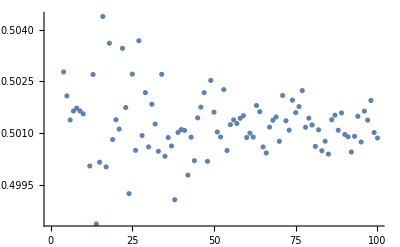

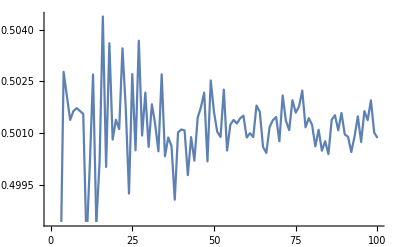

As we can see, the data points converge around the probability of 0.501, or 50.1%, which matches our census result.

### Code Section

```mathematica
currentOdds = 0; (*Declaration for local tempory variable*)
oddsStore = {}; (*List for storing the results at each sample size*)
```

getSample generates i amount of random hands. Then increases the PAIR global variable for each random hand that is a pair.

```mathematica
getSample [i_]:=For[sSize=0,sSize<i,sSize++,getResult[handsF[[RandomInteger[{1, Length[handsF]}]]]]];
```

Runs getSample 100 times to generate 100 samples of i*10000 hands, where i goes from 1 to 100. It then appends the odds of getting a pair in that sample size.

```mathematica
For[i=1,i≤100,i++,PAIR=0;getSample[10000*i];Print[i];currentOdds=PAIR/10000*i;AppendTo[oddsStore, currentOdds]];
```

Result of the above execution. We have collected the data here to not have to re-run the code as it takes some time to execute.

```mathematica
chachedStore={2481/5000,497/1000,14899/30000,20111/40000,1569/3125,30083/60000,7023/14000,20069/40000,11287/22500,12539/25000,54759/110000,10001/20000,5027/10000,17443/35000,1563/3125,80701/160000,21251/42500,90649/180000,19031/38000,50139/100000,21047/42000,110761/220000,115401/230000,1997/4000,62839/125000,130131/260000,45331/90000,140261/280000,145631/290000,150181/300000,15557/31000,32081/64000,165157/330000,4273/8500,43779/87500,4007/8000,185233/370000,11853/23750,65133/130000,200443/400000,205443/410000,6997/14000,215381/430000,22009/44000,4513/9000,230807/460000,118011/235000,240089/480000,35177/70000,62701/125000,255529/510000,260463/520000,266199/530000,270269/540000,137843/275000,35097/70000,28573/57000,29083/58000,295889/590000,4007/8000,305611/610000,6211/12400,63227/126000,321039/640000,325391/650000,330283/660000,83947/167500,4011/8000,57669/115000,43817/87500,356487/710000,18049/36000,73159/146000,46431/92500,125399/250000,190673/380000,386721/770000,390913/780000,79227/158000,12531/25000,135167/270000,410901/820000,25963/51875,28043/56000,53167/106250,86239/172000,145441/290000,88191/176000,111603/222500,150289/300000,56977/113750,460419/920000,77641/155000,2357/4700,118927/237500,6421/12800,486337/970000,10039/20000,496009/990000,250431/500000};
oddsStore=chachedStore;
```

Visual representation of the sample distrubution

```mathematica
ListPlot[oddsStore]
ListLinePlot[oddsStore]
```

-Graphics-

-Graphics-